# Mediator Model Analysis

Isaac R. Wang

This code analysis the freeze-in and out for the mediator model.

## Prepare

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

```mathematica
MakeBoxes[p1,TraditionalForm]:="p_1";
MakeBoxes[p2,TraditionalForm]:="p_2";
MakeBoxes[p3,TraditionalForm]:="p_3";
MakeBoxes[p4,TraditionalForm]:="p_4";
MakeBoxes[mχ,TraditionalForm]:="m_χ";
MakeBoxes[mν,TraditionalForm]:="m_ν";
MakeBoxes[mϕ,TraditionalForm]:="m_ϕ";
MakeBoxes[m1,TraditionalForm]:="m_1";
MakeBoxes[m2,TraditionalForm]:="m_2";
MakeBoxes[yχ,TraditionalForm]:="y_χ";
MakeBoxes[yν,TraditionalForm]:="y_ν";
MakeBoxes[αχ,TraditionalForm]:="α_χ";
MakeBoxes[αν,TraditionalForm]:="α_ν";
MakeBoxes[gH,TraditionalForm]:="g_H";
MakeBoxes[mpl,TraditionalForm]:="m_pl";
MakeBoxes[E1,TraditionalForm]:="E_1";
MakeBoxes[vsq,TraditionalForm]:="v^2";
MakeBoxes[Γϕ,TraditionalForm]:="Γ_ϕ";
```

## Annihilation amplitude

The Lagrangian of the model is

L=y_χ χ̄ ϕ_μ γ^μ P_L χ+y_ν ν̄ ϕ_μ γ^μ P_L ν

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,m1,m1,m2,m2];
M=yχ yν(SpinorVBar[p2,m1].GA[μ].GA[7].SpinorU[p1,m1])MT[μ,ν]/(SP[p1+p2,p1+p2]-mϕ^2+ⅈ mϕ Γϕ)(SpinorUBar[p3,m2].GA[ν].GA[7].SpinorV[p4,m2])//Contract;
Msq=FermionSpinSum[ComplexConjugate[M]*M,ExtraFactor->1/4]//DiracSimplify//Simplify
```

(y_ν^2 y_χ^2 (m_1^2+m_2^2-u)^2)/(s^2+m_ϕ^2 (Γ_ϕ^2-2 s)+m_ϕ^4)

The 2 couplings are always connected with each other here. So this time we just assume they are the same.
One feature of this amplitude is that we are using general m_1 and m_2. In specific status, we should pick which one is which.

```mathematica
(*ν -> χ*)
pi=(√s)/2;
pf=√(s/4-mχ^2);
Msqνtoχ=Msq/.{m1->0,m2->mχ,yν->y,yχ->y,u->mχ^2-2(s/4+pi pf cosθ)};
σ=1/(64 π^2 s)pf/pi Integrate[Msqνtoχ,{cosθ,-1,1}]//Simplify
(*χ -> ν*)
pf=(√s)/2;
pi=√(s/4-mχ^2);
Msqχtoν=Msq/.{m1->mχ,m2->0,yν->y,yχ->y,u->mχ^2-2(s/4+pi pf cosθ)};
σ=1/(64 π^2 s)pf/pi Integrate[Msqχtoν,{cosθ,-1,1}]//Simplify
```

-(y^4 (m_χ^2-s) √(s-4 m_χ^2))/(96 π^2 √s (s^2+m_ϕ^2 (Γ_ϕ^2-2 s)+m_ϕ^4))

(√s y^4 (s-m_χ^2))/(96 π^2 √(s-4 m_χ^2) (s^2+m_ϕ^2 (Γ_ϕ^2-2 s)+m_ϕ^4))

## Estimation: pure analytical approach

### Estimate the benchmark coupling

```mathematica
Cν[y_,T_]:=y^4/(128 π^5)T^4;
nχ[y_,T_]=T^3 mpl/gH Integrate[Cν[y,T‵]/(T‵)^6,{T‵,T,∞}]//Normal
```

(m_pl T^2 y^4)/(128 π^5 g_H)

```mathematica
neq[T_]:=(3 Zeta[3])/(4 π^2)T^3;
```

```mathematica
ymax=y/.Solve[nχ[y,T]==1/10 neq[T],y][[-1]]
```

(2 π^(3/4) g_H^(1/4) T^(1/4) ((3 3)/5)^(1/4))/m_pl^(1/4)

```mathematica
ymax/.{gH->√(8 π^3/90*10.75),mpl->1.22*10^19,T->10^-4}
```

0.0000112405

A little bit more than 10^-5.

### Estimate the equilibrium

```mathematica
Teqsol=T/.Solve[nχ[y,T]==neq[T],T][[-1]]
```

(m_pl y^4)/(96 π^3 g_H 3)

```mathematica
Teqsol/.{y->10^-5,gH->√(8 π^3/90*10.75),mpl->1.22*10^19}
Teqsol/.{y->1.1*10^-5,gH->√(8 π^3/90*10.75),mpl->1.22*10^19}
```

6.26414×10^-6

9.17132×10^-6

The equilibrium temperature is around keV, and very sensitive to the coupling (of course!).

#### How many freeze-out dark matter?

Freeze-out process is relatively code, and the amplitude is roughly

```mathematica
Msq‵fo[y_,mϕ_]=y^4/(32π mϕ^2);
```

Analytical approach to the solution

```mathematica
xfo[y_,mϕ_]=35.5+9.52Log10[y (mϕ gH/17.2)^(-1/4)];
σv[y_,mϕ_]=Msq‵fo[y,mϕ](1-3/xfo[y,mϕ]+6/xfo[y,mϕ]^2);
Ωh[y_,mϕ_]:=0.12 xfo[y,mϕ]/(√10.75)*(1.4*10^-9)/σv[y,mϕ]/.{gH->√(8 π^3/90*10.75),mpl->1.22*10^19};
```

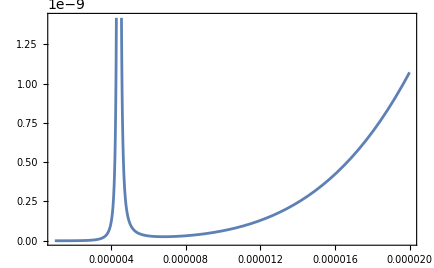

```mathematica
Plot[σv[y,10^-6]/.{gH->√(8 π^3/90*10.75),mpl->1.22*10^19},{y,0.1*10^-5,2*10^-5}]
```

```mathematica
Ωh[10^-5,10^-6]
```

2.71967

```mathematica
ana‵Ω‵data=Flatten[Table[{logmϕ,logy,Ωh[10^logy*10^-5,10^logmϕ*10^-6]},{logmϕ,-2,0,0.02},{logy,-1,Log10[2],0.02}],1];
```

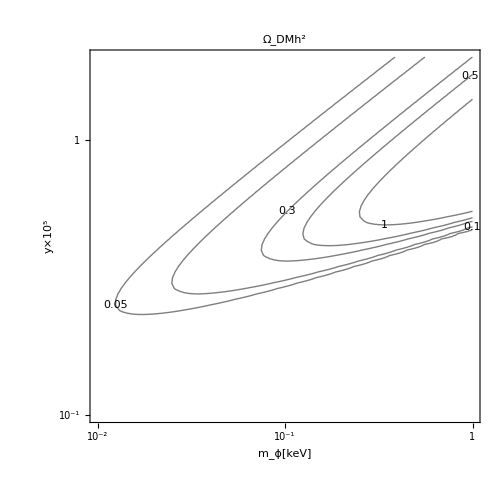

```mathematica
ListContourPlot[ana‵Ω‵data,PlotRange->Full,PlotLegends->Automatic,Contours->{0.05,0.1,0.3,0.5,1.0},BaseStyle->{FontSize->20,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_ϕ[keV]",FontFamily->"Times",FontSize->20],Style["y×10^5",FontFamily->"Times",FontSize->20]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->20],ImageSize->500,FrameTicks->{{LogTicks[-2,1,1],True},{LogTicks[-2,0,1],True}},ContourLabels->True,ContourShading->None,PlotLabel->Style["Ω_DMh^2",FontSize->26,FontFamily->"Times"]]
```

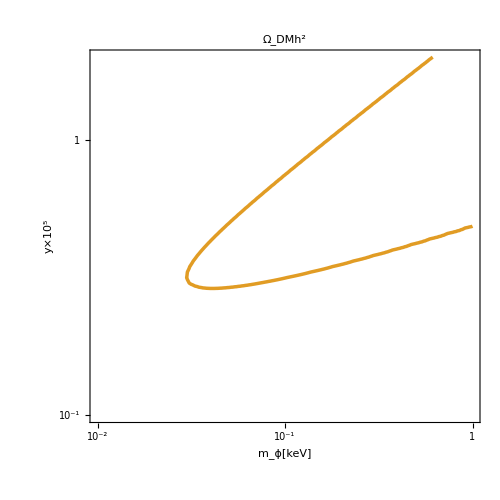

```mathematica
DM‵prod‵plot=ListContourPlot[ana‵Ω‵data,Contours->{0.12},BaseStyle->{FontSize->20,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_ϕ[keV]",FontFamily->"Times",FontSize->20],Style["y×10^5",FontFamily->"Times",FontSize->20]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->20],ImageSize->500,FrameTicks->{{LogTicks[-2,1,1],True},{LogTicks[-2,1,1],True}},ContourShading->None,PlotLabel->Style["Ω_DMh^2",FontSize->26,FontFamily->"Times"],ContourStyle->Directive[Thickness[0.005],ColorData[97,2],Opacity[1.0]]]
```

```mathematica
ΩDM‵ana‵func[logm_,logy_]=Interpolation[ana‵Ω‵data][logm,logy];
```

### What is the PTOLEMY signal?

```mathematica
Φν[m_,y_]:=(y/10^-1)^4(0.1/(2m))^4 1.6*10^8;(*m in unit keV, y in unit 10^-5*);
Γcap[m_,y_]:=10 (Φν[m,y]/(2 10^11));
```

```mathematica
ptodata=Flatten[Table[{logmϕ,logy,Γcap[10^logmϕ,10^logy]},{logmϕ,-2,0,0.02},{logy,-1,Log10[2],0.02}],1];
```

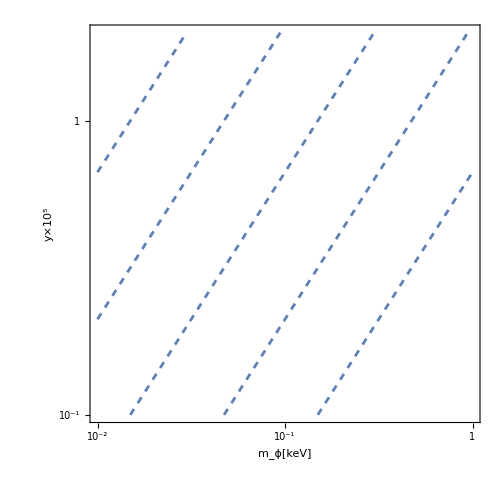

```mathematica
pto‵plot=ListContourPlot[{#1,#2,Log10[#3]}&@@@ptodata,Contours->{-4,-2,0,2,4},BaseStyle->{FontSize->20,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_ϕ[keV]",FontFamily->"Times",FontSize->20],Style["y×10^5",FontFamily->"Times",FontSize->20]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->20],ImageSize->500,FrameTicks->{{LogTicks[-2,1,1],True},{LogTicks[-2,1,1],True}},ContourShading->None,ContourStyle->Directive[ColorData[97,1],Thickness[0.004],Opacity[1.0],Dashed]]
```

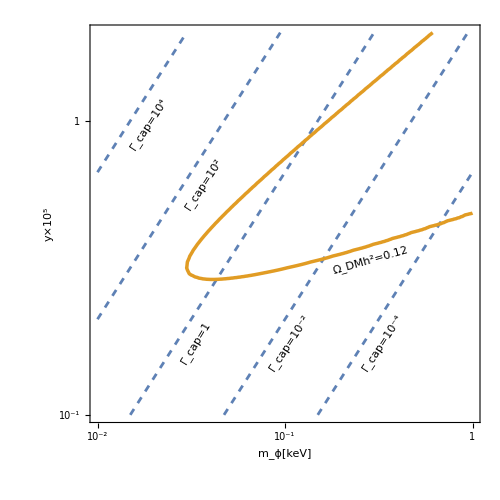

```mathematica
Show[{pto‵plot,DM‵prod‵plot},Epilog->{Inset[Rotate[Framed[Style["Ω_DMh^2=0.12",FontSize->22],FrameStyle->None],16 Degree],Scaled[{0.72,0.41}]],Inset[Rotate[Framed[Style["Γ_cap=10^-4",FontSize->22],FrameStyle->None],57 Degree],Scaled[{0.75,0.2}]],Inset[Rotate[Framed[Style["Γ_cap=10^-2",FontSize->22],FrameStyle->None],57 Degree],Scaled[{0.51,0.2}]],Inset[Rotate[Framed[Style["Γ_cap=1",FontSize->22],FrameStyle->None],59 Degree],Scaled[{0.27,0.2}]],Inset[Rotate[Framed[Style["Γ_cap=10^2",FontSize->22],FrameStyle->None],57 Degree],Scaled[{0.29,0.6}]],Inset[Rotate[Framed[Style["Γ_cap=10^4",FontSize->22],FrameStyle->None],57 Degree],Scaled[{0.15,0.75}]]}]
```

```mathematica
Scaled
```

## A better estimate

An esimation with less approximations, but still an estimation

### Freeze-in

```mathematica
gstarsdata=Import[NotebookDirectory[]<>"gstars.txt","Table"];
gstars[T_]:=Interpolation[gstarsdata][T];
Nν=6;
s[T_]:=gstars[T] (2 π^2)/45 T^3;
MPl=2.44*10^18;(*Reduced planck mass*)
H[T_]:=√(gstars[T]/90)(π/MPl)T^2;
ρSM[T_]:=gstars[T] π^2/30 T^4;
CR[y_,mϕ_,T_]:=1/(64 π^5)Nν (y^2(mϕ^2+2 T^2)^2)/(16 T^4) T^5/;T>=mϕ;(*y means Subscript[y, ν] Subscript[y, χ]*)
CR[y_,mϕ_,T_]:=1/(64 π^5)Nν (y^2(mϕ^2+2 T^2)^2)/mϕ^4 T^5/;T<mϕ;
ρνPower[y_,mϕ_,T_]:=s[T]^(4/3)NIntegrate[CR[y,mϕ,T‵]/(3H[T‵] s[T‵]^(7/3))s'[T‵],{T‵,T,10^7}];
```

```mathematica
ΔNeff[y_,mϕ_,T_]:=4/7 gstars[T](10.75/gstars[T])^(4/3)ρνPower[y,mϕ,T]/ρSM[T]
```

```mathematica
ΔNeff[10^-9.6,10^-6,10^-4]
```

0.462372

Not sensitive to T and m_χ at all! Should scan over coupling and mediator mass.

```mathematica
data=Table[{logyχ,logmϕ,Log10[ΔNeff[10^logyχ,10^logmϕ,10^-4]]},{logyχ,-10,-9,0.1},{logmϕ,-7,-4,0.2}];
```

```mathematica
dataformat=Flatten[data,1];
Export[NotebookDirectory[]<>"Neff_mediator.csv",dataformat];
```

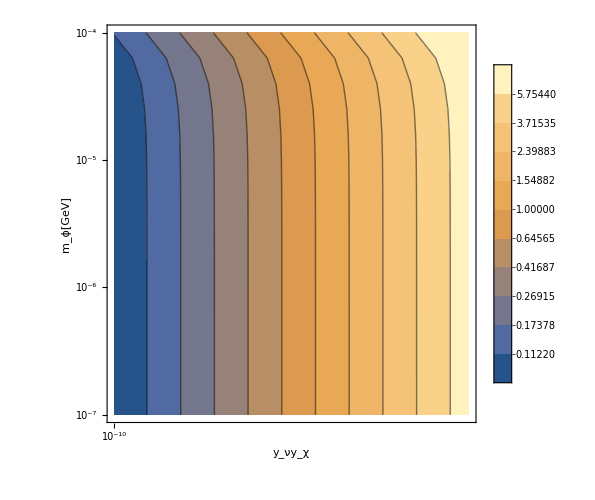

```mathematica
ListContourPlot[{#1,#2,10^#3}&@@@dataformat,PlotRange->Full,PlotLegends->Automatic,ScalingFunctions->"Log10",Contours->10,BaseStyle->{FontSize->20,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["y_νy_χ",FontFamily->"Times",FontSize->20],Style["m_ϕ[GeV]",FontFamily->"Times",FontSize->20]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->20],PlotRangePadding->None,ImageSize->500,FrameTicks->{{LogTicks[-7,-4,1],True},{LogTicks[-14,-4,1],True}}]
```

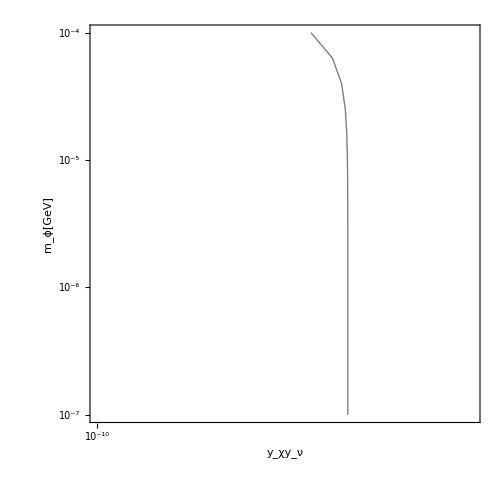

```mathematica
bound=ListContourPlot[{#1,#2,10^#3}&@@@dataformat,PlotRange->Full,ScalingFunctions->"Log10",Contours->{0.2},BaseStyle->{FontSize->20,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["y_χy_ν",FontFamily->"Times",FontSize->20],Style["m_ϕ[GeV]",FontFamily->"Times",FontSize->20]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->20],PlotRangePadding->None,ContourShading->None,ImageSize->500,FrameTicks->{{LogTicks[-7,-4,1],True},{LogTicks[-12,-4,1],True}}]
```

```mathematica
NeffNum[log10yχyν_,log10mϕ_]=Interpolation[{#1,#2,10^#3}&@@@dataformat][log10yχyν,log10mϕ]
```

InterpolatingFunction[…](log10yχyν,log10mϕ)

```mathematica
FindRoot[NeffNum[x,-5]==0.2,{x,-9.2}]
```

{x→-9.78289}

```mathematica
NeffNum[-9.78289,-5]
```

0.199999

```mathematica
ΔNeff[10^-9.78289,10^-5,10^-4]
```

0.20013

```mathematica
y‵ben=x/.FindRoot[NeffNum[x,-5]==0.2,{x,-9.2}];
```

```mathematica
traceT‵data=Table[{logT,Log10[ρνPower[10^(y‵ben),10^-5,10^logT*10^-3]/ρSM[10^logT*10^-3]]},{logT,-9,0,0.2}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in T‵ near {T‵} = {1.10504×10^-11}. NIntegrate obtained 9.03193×10^6 and 93.115 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in T‵ near {T‵} = {0.0000100197}. NIntegrate obtained 2275.39 and 0.00348079 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in T‵ near {T‵} = {0.0000100216}. NIntegrate obtained 1438.13 and 0.00347591 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

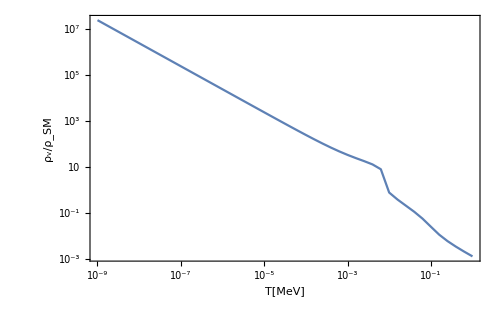

```mathematica
ListLinePlot[traceT‵data,BaseStyle->{FontSize->20,FontFamily->"Times"},Frame->True,FrameLabel->{Style["T[MeV]",FontFamily->"Times",FontSize->20],Style["ρ_v/ρ_SM",FontFamily->"Times",FontSize->20]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->20],PlotRangePadding->None,ImageSize->500,FrameTicks->{{LogTicks[-3,7,1],True},{LogTicks[-9,0,1],True}}]
```

## Careful Treatment

### Freeze-out

```mathematica
MPl=2.44*10^18;(*Reduced planck mass*)
mPl=1.24*10^19;
gstarsdata={#1,#2}&@@@Import[NotebookDirectory[]<>"gstars.txt","Table"];
gstars[T_]:=Interpolation[gstarsdata][T];
gstarsx[x_,mχ_]:=gstars[mχ/x];
s[x_,mχ_]:=((2 π^2)/45)gstarsx[x,mχ](mχ/x)^3;
Yeq[x_,mχ_]:=4 mχ^3/s[x,mχ] x^(-3/2)ⅇ^-x/(2π)^(3/2);
H[x_,mχ_]:=√(gstarsx[x,mχ]/90)(π/MPl)(mχ^2/x^2);
ϵv[y_,v_]:=4 π/y^2 v;
ϵϕ[mχ_,mϕ_,y_]:=4 π/y^2 mϕ/mχ;
S[mχ_,mϕ_,y_,v_]:=(π Sinh[12 ϵv[y,v]/(π ϵϕ[mχ,mϕ,y])])/(ϵv[y,v](Cosh[12 ϵv[y,v]/(π ϵϕ[mχ,mϕ,y])]-Cos[12 ϵv[y,v]/(π ϵϕ[mχ,mϕ,y])√(π^2 ϵϕ[mχ,mϕ,y]/(6 ϵv[y,v]^2)-1)]))//Re
```

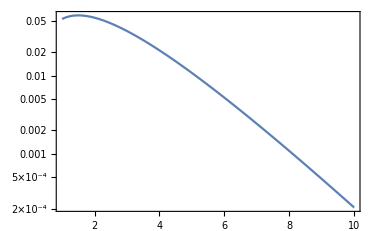

```mathematica
LogPlot[Yeq[x,10^-6],{x,1,10}]
```

```mathematica
FindRoot[D[Yeq[x,10^-6],x],{x,2}]
```

{x→1.5}

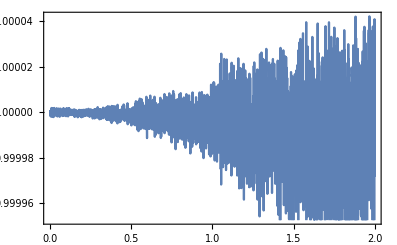

```mathematica
Plot[S[mχtest,mϕtest,ytest,v],{v,0,2}]
```

```mathematica
ytest=0.9*10^-5;
mχtest=.1*10^-6;
mϕtest=.01*10^-6;
σnum=σlinear/.{mχ->mχtest,mϕ->mϕtest,y->ytest};
Normalization[x_]=Integrate[4π v^2 Exp[-x/4 v^2],{v,0,2},Assumptions->{x∈PositiveReals}]//Simplify;
σeffavg[x_]:=1/Normalization[x] NIntegrate[4π v^2 Exp[-x/4 v^2]σnum S[mχtest,mϕtest,ytest,v],{v,0,2}];
Savg[x_]:=1/Normalization[x] NIntegrate[4π v^2 Exp[-x/4 v^2]S[mχtest,mϕtest,ytest,v],{v,0,2}];
σlist=Table[{logx,Log10[σeffavg[10^logx]]},{logx,0,7,0.2}];
func[logx_]=10^Interpolation[σlist][logx];
σeff[x_]=func[Log10[x]];
Δ[mχ_]:=NIntegrate[σeff[x]/x^2 √gstarsx[x,mχ] √(90/π^2)(2 π^2)/45 mχ MPl,{x,100,10^7}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {1.80856}. NIntegrate obtained 2.01303×10^-8 and 7.3056×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {1.76559}. NIntegrate obtained 1.5612×10^-8 and 5.21368×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {1.59763}. NIntegrate obtained 1.09072×10^-8 and 3.0591×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: exp(-1000.) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: exp(-1584.89) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: exp(-2511.89) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.995595} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

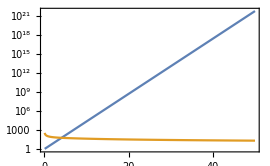

4.09116

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {8.68678}. NIntegrate obtained 3.53367×10^-10 and 2.54858×10^-15 for the integral and error estimates.

0.121682

```mathematica
LogPlot[{ⅇ^x,(√(45/8)4mχtest mPl σeff[x])/(2 π^3 √gstarsx[x,mχtest] √x)},{x,0.1,50}]
xf=x/.FindRoot[ⅇ^x==(√(45/8)4mχtest mPl σeff[x])/(2 π^3 √gstarsx[x,mχtest] √x),{x,1}]
σf=NIntegrate[σeff[x]/x^2,{x,xf,10^7}];
ΩDMhsq=1.07*10^9/(√gstarsx[xf,mχtest] mPl σf)
```

{{lnY→InterpolatingFunction[…]}}

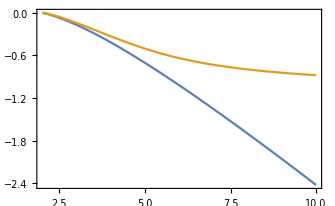

{0.115425}

```mathematica
boundary=2;
sol=NDSolve[{ⅇ^lnY[x] lnY'[x]==(-σeff[x])/(H[x,mχtest]x)s[x,mχtest](ⅇ^lnY[x]-Yeq[x,mχtest])(ⅇ^lnY[x]+Yeq[x,mχtest]),lnY[boundary]==Log[Yeq[boundary,mχtest]]},lnY,{x,boundary,100}]
Plot[{Log10[Yeq[x,mχtest]/ⅇ^lnY[boundary]]/.sol,Log10[(ⅇ^(lnY[x]-lnY[boundary]))/.sol]},{x,boundary,10}]
Yf=ⅇ^lnY[100]/.sol;
Yinf=Yf/(1+Yf Δ[mχtest]);
s0=2891.2;
ρDM0=s0 mχtest Yinf;
ρcrit=1.05*10^-5;
ΩDMhsq=ρDM0/ρcrit
```